```mathematica
SetDirectory[NotebookDirectory[]]
rasterizeBackground[g_,res_: 100]:=Show[Graphics[{Inset[Rasterize[Show[g,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]]}],Sequence@@Options[g],Sequence@@AbsoluteOptions[g,PlotRange],Sequence@@Options[g,Epilog]]
```

/home/zack/cantera/ratematrix

data/parallelgri1

{12,130,3,16910,7}

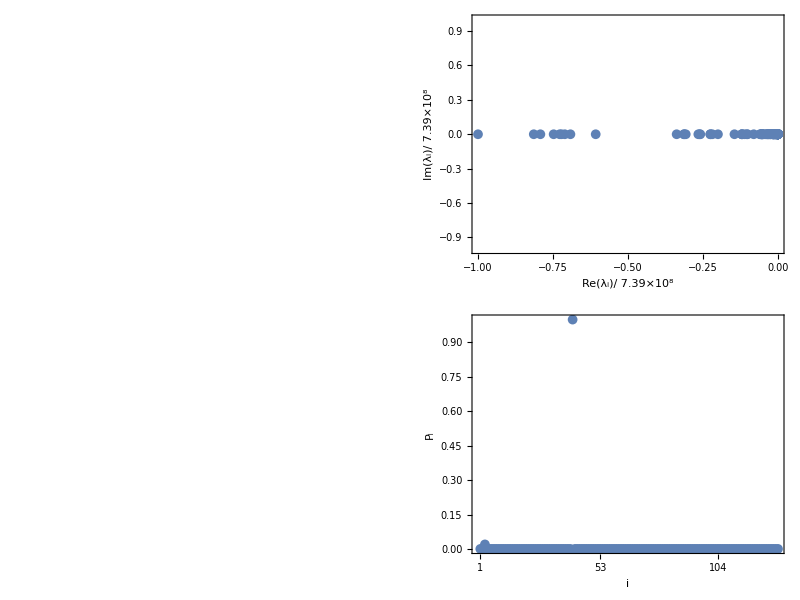

plots/example.pdf

{Ar_1+N_2+2 (O_1 H_2)+O_2 C_1,Ar_1+2 (H_2)+O_1 N_1+O_1 C_1+O_2 N_1,Ar_1+N_1+2 (H_2)+O_2 N_1+O_2 C_1,Ar_1+H_2+O_1 N_1+O_1 H_2 C_1+O_2 N_1,Ar_1+N_2+O_1+O_1 C_1+2 (O_1 H_2)}

{5634.81,933.601,207.272,918.983,3155.36}

{3.75654,0.746881,0.165818,0.612655,2.52429}

```mathematica
filebase="data/parallelgri1"
dat=Import[filebase<>"out.dat"];
{atoms, dim,runtime, count, level} = dat[[1,1;;5]]
elements=dat[[3]];
A=Transpose[Partition[BinaryReadList[filebase<>"ratematrix.npy","Real64"][[17;;-1]],dim]];
evals=#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2];
evecs=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvectors.npy","Real64"][[17;;-1]],2],dim];
temperatures=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
spatoms=Partition[BinaryReadList[filebase<>"spatoms.npy","Integer64"][[17;;-1]],Length[elements]];
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],Length[spatoms]];
spforms=Table[DisplayForm[RowBox[Table[If[spatoms[[i,j]]>0,Subscript[elements[[j]],spatoms[[i,j]]],""],{j,1,Length[elements]}]]],{i,1,Length[spatoms]}];
multiforms=Table[Total[multiindices[[i]]*spforms],{i,1,dim}];
p=Grid[{{rasterizeBackground[MatrixPlot[A,ImageSize->350,FrameTicks->{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[Round[i],{i,1,dim,(dim-1)/5}]},FrameLabel->{{i,"Rate matrix"},{j,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{105,25},{65,65}}]],ListPlot[{Re[#]/Max[Abs[evals]],Im[#]/Max[Abs[evals]]}&/@evals,ImageSize->350,PlotRange->All,AspectRatio->1,Axes->False,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{{DisplayForm[RowBox[{Im[Subscript[λ,i]],"/",PaddedForm[Max[Abs[evals]],3]}]],None},{DisplayForm[RowBox[{Re[Subscript[λ,i]],"/",PaddedForm[Max[Abs[evals]],3]}]],Eigenvalues}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->Directive[PointSize[0.02]],ImagePadding->{{105,25},{65,65}}]},{rasterizeBackground[MatrixPlot[Reverse[evecs],ImageSize->350,FrameTicks->{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[Round[i],{i,1,dim,(dim-1)/5}]},FrameLabel->{{i,"Left eigenvectors"},{j,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{105,25},{65,65}}]],ListPlot[Abs[evecs[[-1]]],ImageSize->350,PlotRange->All,Axes->False,Frame->True,FrameLabel->{{Subscript[P,i],None},{i,"Steady distribution"}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[Round[i],{i,1,dim,(dim-1)/5}],None}},PlotStyle->Directive[PointSize[0.02]],ImagePadding->{{105,25},{65,65}}]}}]
Export["plots/example.pdf",p]
multiforms[[Reverse[Ordering[Abs[evecs[[-1]]]]]]][[1;;5]]
temperatures[[Reverse[Ordering[Abs[evecs[[-1]]]]]]][[1;;5]]
pressures[[Reverse[Ordering[Abs[evecs[[-1]]]]]]][[1;;5]]
```

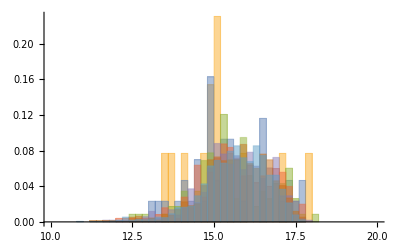

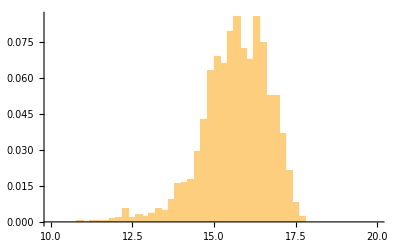

```mathematica
dims=Table[Import["data/h2o2"<>ToString[i]<>"out.dat"][[1,2]],{i,2,8}];sevals=Table[Abs[#[[1]]+I*#[[2]]]/dims[[i-1]]^(1/2)&/@Partition[BinaryReadList["data/h2o2"<>ToString[i]<>"eigenvalues.npy","Real64"][[17;;-1]],2],{i,2,8}];
Histogram[Log[sevals], {10,20,0.2},"Probability"]
Histogram[Log[sevals[[-1]]], {10,20,0.2},"Probability"]
```

## Runtimes

{{9,19,0.0115093,332,9},{12,48,0.0813439,1225,12},{15,89,0.596218,3588,15},{18,177,4.28785,9583,18},{21,298,24.6733,22616,21},{24,516,133.293,50049,24},{27,807,644.169,102480,27}}

{{9,19,0.00166631,332,9},{12,48,0.00269243,1225,12},{15,89,0.0115599,3588,15},{18,177,0.0219312,9583,18},{21,298,0.0630814,22616,21},{24,516,0.150859,50049,24},{27,807,0.324891,102480,27},{30,1277,0.721812,200145,30},{33,1888,1.35229,370476,33},{36,2803,2.49359,661388,36},{39,3965,4.5473,1135106,39},{42,5612,7.90772,1893255,42},{45,7663,12.9912,3063616,45},{48,10450,21.2463,4844184,48},{51,13862,32.9121,7477740,51},{54,18348,51.2392,11324874,54},{57,23760,78.78,16818920,57},{60,30688,113.308,24581466,60}}

{{9,19,0,83,3},{12,48,0,245,4},{15,89,0,598,5},{18,177,1,1369,6},{21,298,2,2827,7},{24,516,1,5561,8},{27,807,2,10248,9},{30,1277,3,18195,10},{33,1888,4,30873,11},{36,2803,3,50876,12},{39,3965,5,81079,13},{42,5612,6,126217,14},{45,7663,6,191476,15},{48,10450,7,284952,16},{51,13862,8,415430,17},{54,18348,9,596046,18},{57,23760,10,840946,19},{60,30688,10,1170546,20},{63,38940,12,1606694,21},{66,49274,13,2180000,22},{69,61446,14,2923048,23},{72,76411,15,3880353,24},{75,93864,17,5099087,25},{78,114989,18,6642312,26},{81,139411,20,8576593,27},{84,168576,21,10989255,28},{87,202029,23,13972160,29},{90,241515,26,17643841,30},{93,286488,28,22128615,31},{96,339030,30,27584561,32},{99,398493,32,34177030,33},{102,467337,35,42113553,34},{105,544800,38,51610691,35},{108,633763,41,62937086,36},{111,733337,45,76372469,37},{114,846870,49,92260201,38},{117,973333,54,110957124,39},{120,1116588,59,132897080,40}}

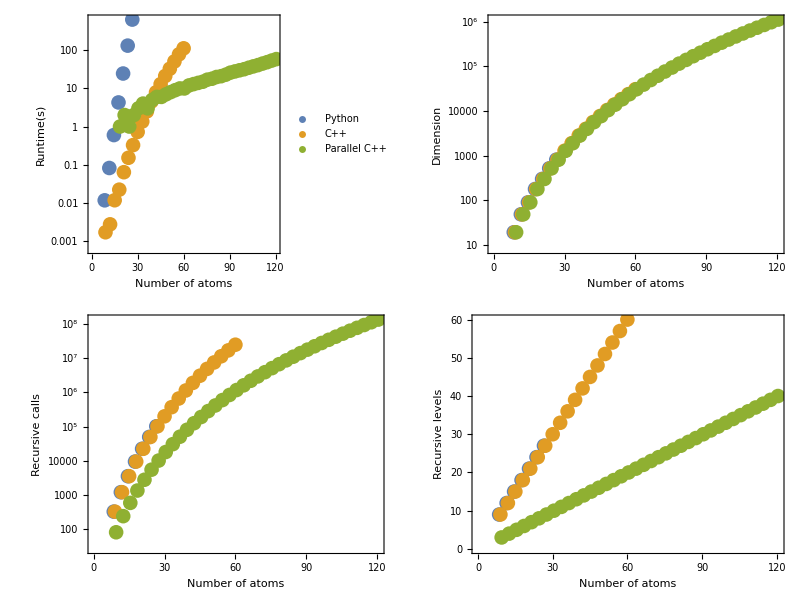

plots/runtimes.pdf

```mathematica
dat=Import["data/runtimesout.dat"]
dat2=Import["data/runtimes2out.dat"]
dat3=Import["data/runtimes3out.dat"]
p=Legended[Grid[{{ListLogPlot[{{#[[1]]-0.5,#[[2]]}&/@dat[[All,{1,3}]],{#[[1]]+0.0,#[[2]]}&/@dat2[[All,{1,3}]],{#[[1]]+0.5,#[[2]]}&/@dat3[[All,{1,3}]]},ImageSize->350,AspectRatio->1,Frame->True,Axes->False,FrameLabel->{"Number of atoms","Runtime(s)"}, FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[16,Black],PlotStyle->Directive[PointSize[0.03]]],ListLogPlot[{{#[[1]]-0.5,#[[2]]}&/@dat[[All,{1,2}]],{#[[1]]+0.0,#[[2]]}&/@dat2[[All,{1,2}]],{#[[1]]+0.5,#[[2]]}&/@dat3[[All,{1,2}]]},ImageSize->350,AspectRatio->1,Frame->True,Axes->False,FrameLabel->{"Number of atoms","Dimension"}, FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[16,Black],PlotStyle->Directive[PointSize[0.03]]]},{ListLogPlot[{{#[[1]]-0.5,#[[2]]}&/@dat[[All,{1,4}]],{#[[1]]+0.0,#[[2]]}&/@dat2[[All,{1,4}]],{#[[1]]+0.5,#[[2]]}&/@dat3[[All,{1,4}]]},ImageSize->350,AspectRatio->1,Frame->True,Axes->False,FrameLabel->{"Number of atoms","Recursive calls"}, FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[16,Black],PlotStyle->Directive[PointSize[0.03]]],ListPlot[{{#[[1]]-0.5,#[[2]]}&/@dat[[All,{1,5}]],{#[[1]]+0.0,#[[2]]}&/@dat2[[All,{1,5}]],{#[[1]]+0.5,#[[2]]}&/@dat3[[All,{1,5}]]},ImageSize->350,AspectRatio->1,Frame->True,Axes->False,FrameLabel->{"Number of atoms","Recursive levels"}, FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[16,Black],PlotStyle->Directive[PointSize[0.03]]]}}],Placed[PointLegend[ColorData[97,"ColorList"][[1;;3]],{"Python","C++","Parallel C++"},LegendMarkerSize->20],Right]]
Export["plots/runtimes.pdf",p]
```

## Temperature - pressure sweep

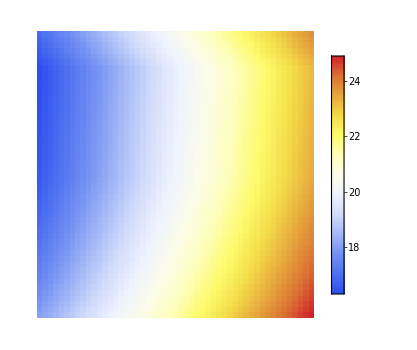
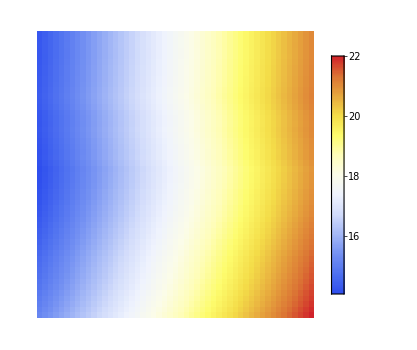
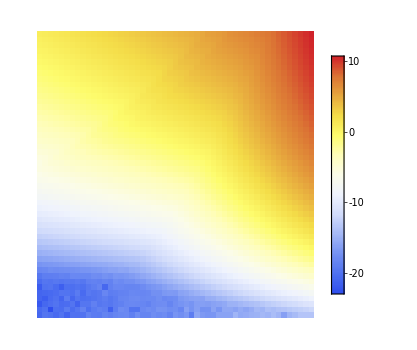
-Graphics- | -Graphics- | -Graphics-

plots/sweep.pdf

```mathematica
press0=0.01;
press1=10.0;
temp0=600;
temp1=2000;
ntemp=50;
npres=50;
sweep=Import["data/sweep1out.dat"];
p=Grid[{{ArrayPlot[Transpose[Partition[Log[Abs[Min[#[[4;;-2]]]]]&/@sweep,ntemp+1]],DataReversed->{True,False},ColorFunction->"TemperatureMap",ImageSize->350,LabelStyle->Directive[16,Black],FrameLabel->{{"Temperature (k)",Log[-Subscript[λ,-1]]},{"Log10 Pressure/(1atm)",None}},FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameTicks->{{Table[{i+1,Log[press0*(press1/press0)^(i/npres)]/Log[10]},{i,0,npres,npres/5}],None},{Table[{i+1,temp0+(temp1-temp0)*i/ntemp},{i,0,ntemp,ntemp/5}],None}},PlotLegends->True],ArrayPlot[Transpose[Partition[Log[Abs[Median[#[[4;;-2]]]]]&/@sweep,ntemp+1]],DataReversed->{True,False},ColorFunction->"TemperatureMap",ImageSize->350,LabelStyle->Directive[16,Black],FrameLabel->{{"Temperature (k)",Log[-OverBar[λ]]},{"Log10 Pressure/(1atm)",None}},FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameTicks->{{Table[{i+1,Log[press0*(press1/press0)^(i/npres)]/Log[10]},{i,0,npres,npres/5}],None},{Table[{i+1,temp0+(temp1-temp0)*i/ntemp},{i,0,ntemp,ntemp/5}],None}},PlotLegends->True],ArrayPlot[Transpose[Partition[Log[Abs[#[[-9]]]]&/@sweep,ntemp+1]],DataReversed->{True,False},ColorFunction->"TemperatureMap",ImageSize->350,LabelStyle->Directive[16,Black],FrameLabel->{{"Temperature (k)",Log[-Subscript[λ,1]]},{"Log10 Pressure/(1atm)",None}},FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameTicks->{{Table[{i+1,Log[press0*(press1/press0)^(i/npres)]/Log[10]},{i,0,npres,npres/5}],None},{Table[{i+1,temp0+(temp1-temp0)*i/ntemp},{i,0,ntemp,ntemp/5}],None}},PlotLegends->True]}}]
Export["plots/sweep.pdf",p]
```

```mathematica
Length[Import["data/sweepout.dat"]]
```

1365

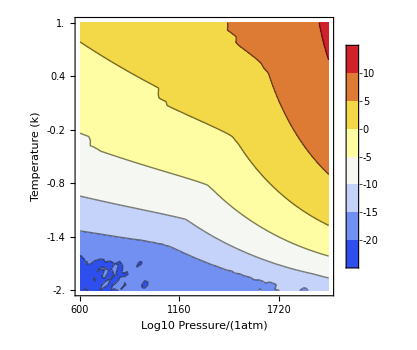

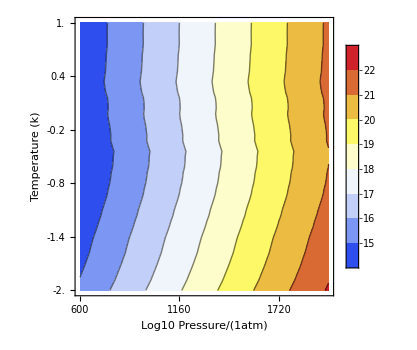

```mathematica
ListContourPlot[Transpose[Partition[Log[Abs[#[[-9]]]]&/@sweep,ntemp+1]],ColorFunction->"TemperatureMap",ImageSize->350,LabelStyle->Directive[16,Black],FrameLabel->{{"Temperature (k)",Log[-Subscript[λ,1]]},{"Log10 Pressure/(1atm)",None}},FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameTicks->{{Table[{i+1,Log[press0*(press1/press0)^(i/npres)]/Log[10]},{i,0,npres,npres/5}],None},{Table[{i+1,temp0+(temp1-temp0)*i/ntemp},{i,0,ntemp,ntemp/5}],None}},PlotLegends->True]
ListContourPlot[Transpose[Partition[Log[Abs[Median[#[[4;;-2]]]]]&/@sweep,ntemp+1]],ColorFunction->"TemperatureMap",ImageSize->350,LabelStyle->Directive[16,Black],FrameLabel->{{"Temperature (k)",Log[-OverBar[λ]]},{"Log10 Pressure/(1atm)",None}},FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameTicks->{{Table[{i+1,Log[press0*(press1/press0)^(i/npres)]/Log[10]},{i,0,npres,npres/5}],None},{Table[{i+1,temp0+(temp1-temp0)*i/ntemp},{i,0,ntemp,ntemp/5}],None}},PlotLegends->True]
```